```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/sec_int_data/412nm.dat"]
```

{{1.63065,-0.196489},{1.58758,-0.183466},{1.51023,-0.148245},{1.46132,-0.122993},{1.41705,-0.105449},{1.38078,-0.0889952},{1.34407,-0.0647412},{1.30453,-0.0587208},{1.27782,-0.0471231},{1.24828,-0.0298099},{1.22646,-0.0217345},{1.20042,-0.0168105},{1.183,-0.000520135},{1.16401,-0.011688},{1.14739,-0.00144104},{1.13423,0.00169856},{1.12389,-0.00920221},{1.11401,-0.230609},{1.10574,-0.0754134},{1.09905,-0.114244},{1.09389,-0.134801},{1.08918,-0.0508302},{1.08895,-0.039937},{1.08874,-0.0243439},{1.08738,-0.00714547},{1.08767,0.0205866},{1.08994,0.0141987},{1.0948,0.0309171},{1.10288,0.0318862},{1.1168,0.0312079},{1.12832,-0.0113947},{1.1517,0.0199007},{1.18117,-0.00827414},{1.20042,0.00796817},{1.25083,-0.0110003},{1.28067,-0.0271143},{1.3108,-0.0233096},{1.33715,-0.0414055}}

0.275578-0.263143 x

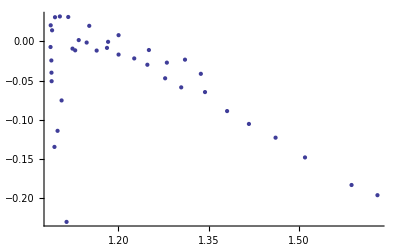

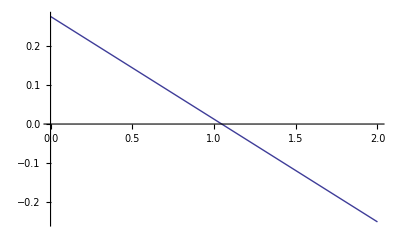

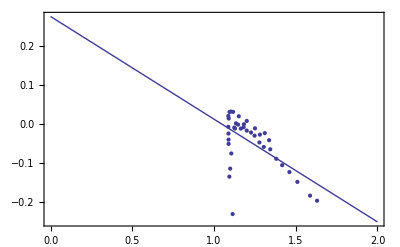

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```